{{ψ→InterpolatingFunction[{{0., 15.}, {…, -60., 60., …}}, <>]}}

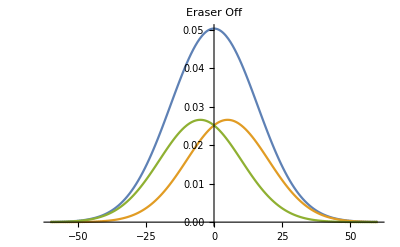

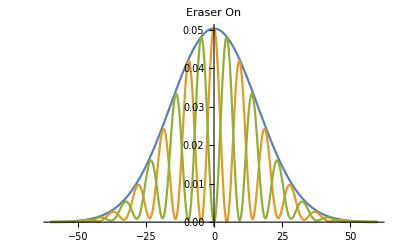

```mathematica
ћ=1;
m=1;
z=5;
ψ0=ⅇ^(-x^2) (2/π)^(1/4);
s=NDSolve[{I*ћ*D[ψ[t,x],t]==-((ћ^2)/(2*m))*D[ψ[t,x],x,x],ψ[t,-60]==ψ[t,60],ψ[0,x]==ψ0},ψ,{t,0,15},{x,-60,60},AccuracyGoal->10]

Plot[{(Abs[ψ[15,x-z]]^2+Abs[ψ[15,x+z]]^2)/.s,Abs[ψ[15,x-z]]^2/.s,Abs[ψ[15,x+z]]^2/.s},{x,-60,60},PlotPoints->150,PlotRange->Full,PlotLabel->"Eraser Off"]
Plot[{(Abs[(ψ[15,x-z]+ψ[15,x+z])/Sqrt[2]]^2+Abs[I(ψ[15,x-z]-ψ[15,x+z])/Sqrt[2]]^2)/.s,Abs[(ψ[15,x-z]+ψ[15,x+z])/Sqrt[2]]^2/.s,Abs[I(ψ[15,x-z]-ψ[15,x+z])/Sqrt[2]]^2/.s},{x,-60,60},PlotPoints->150,PlotRange->Full,PlotLabel->"Eraser On"]
```